## SimInterpolate-example.nb

Example Cellzilla2D notebook
GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

Cellzilla2D (3.0.51f (14 June 2017)) loaded Wed 14 Jun 2017 14:53:36
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

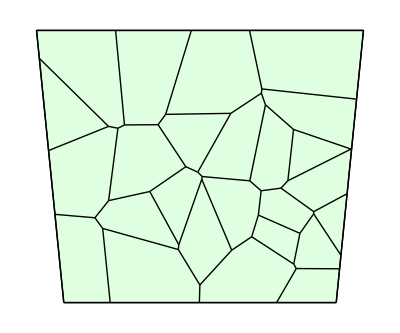

```mathematica
<<Cellzilla2D.m
w=TemplateRandom[25, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
ShowTissue[w]
```

## Set up a model and run a simulation

```mathematica
n=NTissueCells[w]; 
net={{∅⇄A,k1, k2},{2 A+B->3 A,k3},{A->B,k4}};
parameters={k1-> .1, k2-> .1, k3-> .1 ,k4-> .3};
ic[i_]:={A[i]->RandomReal[{0,5}],B[i]->RandomReal[{0,5}]};
myic=Flatten[ic/@Range[n]]
```

{A[1]→2.10572,B[1]→3.20028,A[2]→1.06456,B[2]→4.44736,A[3]→1.71056,B[3]→0.0228016,A[4]→4.05082,B[4]→0.549387,A[5]→3.51074,B[5]→2.04845,A[6]→1.63466,B[6]→0.173094,A[7]→3.53186,B[7]→3.16066,A[8]→1.44289,B[8]→0.237664,A[9]→1.15501,B[9]→0.279315,A[10]→0.738385,B[10]→3.55815,A[11]→1.23951,B[11]→1.21329,A[12]→3.09153,B[12]→3.25543,A[13]→3.72895,B[13]→0.634159,A[14]→1.50215,B[14]→1.33836,A[15]→3.014,B[15]→3.46961,A[16]→4.3628,B[16]→4.15233,A[17]→2.24155,B[17]→4.84364,A[18]→4.55507,B[18]→1.43559,A[19]→4.99359,B[19]→0.914815,A[20]→2.1616,B[20]→0.264978,A[21]→4.40359,B[21]→0.349996,A[22]→0.112248,B[22]→1.84263,A[23]→1.7807,B[23]→3.2275,A[24]→1.74238,B[24]→3.56411,A[25]→3.60652,B[25]→1.07241}

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net,"Diffusion"-> {{A, DA}, {B,DB}}];
```

25 Cells.

4 internal reactions in each cell.

100 intracellular reactions.

232 diffusion reactions.

332 total reactions.

```mathematica
sim=RunSim[bignet/.{DB->.05, DA-> .1},parameters,myic,{0,50}];
```

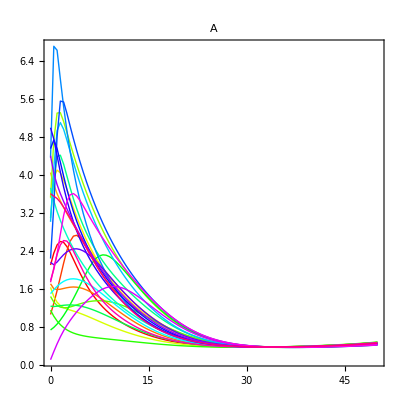
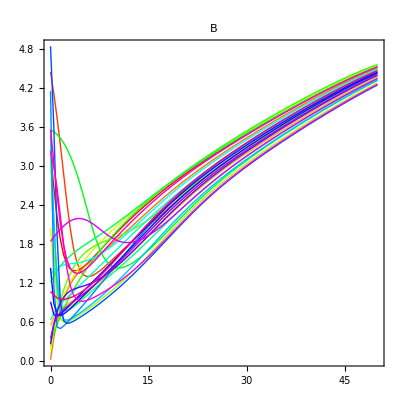

```mathematica
SimPlot[sim]
```

## Use Sim Interpolate to get all values of A at a specific time

```mathematica
SimInterpolate[sim, A, 10]
```

{0.979243,1.54091,1.17369,1.70727,1.65597,0.773294,2.32139,1.30073,0.530084,2.17469,0.948253,1.83682,1.32533,1.26273,2.14217,1.58869,2.44319,1.57858,1.48005,1.71387,1.62471,1.65209,2.27457,1.08151,1.49848}

## Use SimInterpolate to Make a table of Values

```mathematica
TableForm[Prepend[SimInterpolate[sim, A, #], #]&/@Range[0,10,2]]
```

0 | 2.10572 | 1.06456 | 1.71056 | 4.05082 | 3.51074 | 1.63466 | 3.53186 | 1.44289 | 1.15501 | 0.738385 | 1.23951 | 3.09153 | 3.72895 | 1.50215 | 3.014 | 4.3628 | 2.24155 | 4.55507 | 4.99359 | 2.1616 | 4.40359 | 0.112248 | 1.7807 | 1.74238 | 3.60652
2 | 2.58127 | 2.14366 | 1.61164 | 3.31723 | 3.88872 | 1.20986 | 5.12549 | 1.20575 | 0.788455 | 1.04339 | 1.25799 | 4.22765 | 2.87621 | 1.76143 | 4.96187 | 5.43899 | 5.53632 | 3.97377 | 3.7479 | 2.32272 | 3.44227 | 0.722702 | 3.14573 | 2.62026 | 3.32153
4 | 2.07851 | 2.73058 | 1.63898 | 2.8373 | 3.11886 | 1.11349 | 4.21695 | 1.26583 | 0.650158 | 1.53292 | 1.25513 | 3.29034 | 2.32963 | 1.80806 | 4.03726 | 3.76014 | 4.51489 | 3.02764 | 2.82355 | 2.44615 | 2.86807 | 1.11865 | 3.55639 | 2.25608 | 2.83785
6 | 1.57126 | 2.34067 | 1.54799 | 2.4155 | 2.49217 | 1.00617 | 3.45178 | 1.33832 | 0.592476 | 2.06873 | 1.18703 | 2.64172 | 1.91488 | 1.68779 | 3.26044 | 2.73794 | 3.65983 | 2.39489 | 2.23205 | 2.30602 | 2.38264 | 1.40777 | 3.11082 | 1.72369 | 2.33847
8 | 1.22003 | 1.88005 | 1.37475 | 2.03984 | 2.02157 | 0.886515 | 2.82994 | 1.35105 | 0.558731 | 2.31882 | 1.07642 | 2.18685 | 1.5883 | 1.48549 | 2.64147 | 2.06374 | 2.98499 | 1.93684 | 1.80957 | 2.02658 | 1.97167 | 1.60077 | 2.6662 | 1.34522 | 1.88052
10 | 0.979243 | 1.54091 | 1.17369 | 1.70727 | 1.65597 | 0.773294 | 2.32139 | 1.30073 | 0.530084 | 2.17469 | 0.948253 | 1.83682 | 1.32533 | 1.26273 | 2.14217 | 1.58869 | 2.44319 | 1.57858 | 1.48005 | 1.71387 | 1.62471 | 1.65209 | 2.27457 | 1.08151 | 1.49848